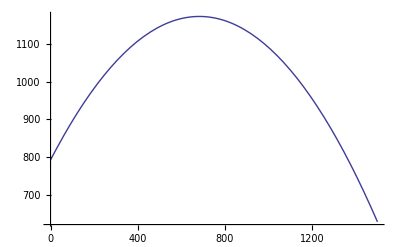

```mathematica
Plot[792.1+1.12*T-8.2*10^-4*T*T,{T,0,1500}]
```

```mathematica
GradientFilter[-Graphics-,10,"NonMaxSuppression"->False]// Binarize
MorphologicalPerimeter[-Graphics-,0.6]
```

-Graphics-

-Graphics-

```mathematica
Manipulate[MorphologicalPerimeter[-Graphics-,a,CornerNeighbors-> False],{a,0,1}]
```

```mathematica
Manipulate[GradientFilter[-Graphics-,a,"NonMaxSuppression"->True]// Binarize//ColorNegate,{a,0,100}]
```

```mathematica
noisy=-Graphics-;
dwd=DiscreteWaveletTransform[noisy,CDFWavelet[]];
thr=WaveletThreshold[dwd,"SmoothGarrote"];
{Labeled[noisy,Text@"original"],Labeled[InverseWaveletTransform[thr],Text@"smoothed"]}
```

{-Graphics-original,-Graphics-smoothed}

```mathematica
{-Graphics-"original",-Graphics-"smoothed"}
```